```mathematica
ClearAll["Global`*"]
```

```mathematica
read[name_]:=Flatten[Import[name,"Table"]];
files=FileNames["*.bin",NotebookDirectory[]];
Do[Print[files[[i]]],{i,1,Length[files]}]
```

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/ENER.bin

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/ENER-Ge-BM.bin

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/STRE.bin

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/STRE-Ge-BM.bin

```mathematica
energyExp=read[files[[1]]];
energyTh=read[files[[2]]];
strengthEx=read[files[[3]]];
strengthTh=read[files[[4]]];
makedata[x_,y_]:=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
isotope=Row[{Superscript["","76"],"Ge"}];
```

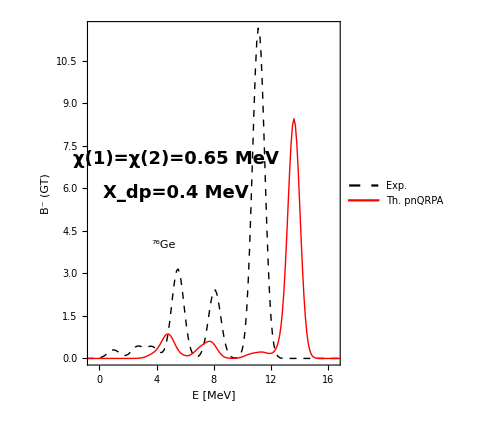

```mathematica
fig1=ListPlot[{makedata[energyExp,strengthEx],makedata[energyTh,strengthTh]},Joined->True,ImageSize->Medium,AspectRatio->1.2,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{20,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"Exp.","Th. pnQRPA"},{0.35,0.8}],Epilog->{Inset[Style["χ(1)=χ(2)=0.65 MeV",18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.6}]],Inset[Style["X_dp=0.4 MeV",18,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.5}]],Inset[Framed[Style[isotope,20,Bold,Black,FontFamily->"Times"]],Scaled[{0.3,0.35}]]},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},PlotRange->{{-0.5,16.5},Full}];
Show[fig1]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/76Ge/STRE-Ge-BM.pdf",Show[fig1],ImageResolution->1200];
```

```mathematica
{0.00002,0.00004,0.00011,0.00027,0.00064,0.00142,0.00298,0.00593,0.01115,0.01985,0.03344,0.05328,0.0803,0.11452,0.15449,0.19719,0.23811,0.27202,0.29403,0.30075,0.29123,0.26724,0.23295,0.19406,0.15673,0.12659,0.10817,0.10454,0.11722,0.14604,0.18895,0.24189,0.29895,0.3531,0.3974,0.42664,0.43877,0.43558,0.42237,0.40641,0.39472,0.39194,0.3988,0.41195,0.42507,0.43088,0.42344,0.39997,0.36177,0.31403,0.26499,0.225,0.20583,0.22042,0.28282,0.40742,0.60685,0.88831,1.24857,1.66962,2.11661,2.54049,2.8856,3.1011,3.15305,3.03298,2.76012,2.37632,1.93554,1.49148,1.08734,0.75004,0.48973,0.30319,0.17922,0.10402,0.0653,0.05489,0.06989,0.11275,0.19045,0.3127,0.48896,0.72451,1.016,1.34803,1.69213,2.00951,2.25768,2.39968,2.41302,2.29555,2.066,1.7591,1.417,1.07986,0.77854,0.53102,0.34267,0.20922,0.12094,0.06639,0.03521,0.01959,0.0151,0.02111,0.04167,0.08712,0.17625,0.33876,0.61646,1.06145,1.7291,2.66479,3.88529,5.35922,6.99354,8.63396,10.08419,11.14267,11.6481,11.51964,10.77804,9.54022,7.98905,6.3292,4.74373,3.36364,2.2564,1.43199,0.85977,0.48836,0.26243,0.13342,0.06417,0.0292,0.01257,0.00512,0.00197,0.00072,0.00025,0.00008,0.00002,0.00001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}-{0.00002,0.00004,0.00011,0.00027,0.00064,0.00142,0.00298,0.00593,0.01115,0.01985,0.03344,0.05328,0.0803,0.11452,0.15449,0.19719,0.23811,0.27202,0.29403,0.30075,0.29123,0.26724,0.23295,0.19406,0.15673,0.12659,0.10817,0.10454,0.11722,0.14604,0.18895,0.24189,0.29895,0.3531,0.3974,0.42664,0.43877,0.43558,0.42237,0.40641,0.39472,0.39194,0.3988,0.41195,0.42507,0.43088,0.42344,0.39997,0.36177,0.31403,0.26499,0.225,0.20583,0.22042,0.28282,0.40742,0.60685,0.88831,1.24857,1.66962,2.11661,2.54049,2.8856,3.1011,3.15305,3.03298,2.76012,2.37632,1.93554,1.49148,1.08734,0.75004,0.48973,0.30319,0.17922,0.10402,0.0653,0.05489,0.06989,0.11275,0.19045,0.3127,0.48896,0.72451,1.016,1.34803,1.69213,2.00951,2.25768,2.39968,2.41302,2.29555,2.066,1.7591,1.417,1.07986,0.77854,0.53102,0.34267,0.20922,0.12094,0.06639,0.03521,0.01959,0.0151,0.02111,0.04167,0.08712,0.17625,0.33876,0.61646,1.06145,1.7291,2.66479,3.88529,5.35922,6.99354,8.63396,10.08419,11.14267,11.6481,11.51964,10.77804,9.54022,7.98905,6.3292,4.74373,3.36364,2.2564,1.43199,0.85977,0.48836,0.26243,0.13342,0.06417,0.0292,0.01257,0.00512,0.00197,0.00072,0.00025,0.00008,0.00002,0.00001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}